```mathematica
ClearAll["Global`*"];
Lmin = 0;
Lmax = +1;
Vmin = -10;
Vmax = +10;
nx = 1;
kx = 2 Pi/((Lmax - Lmin)/nx);
nv = 2;
kv =  2 Pi/((Vmax - Vmin)/nv);
w =1;
LevX=4;
LevV=4;
Deg=3;
dt=N[Lmax/(2^LevX)/Vmax(2*Deg+1)]
nt=100;
fx:= Sin[kx x ];
ft:= Sin[w t];
fv:= Sin[kv v];
f:=fx fv ft;
Ex:=Cos[kx x];
Et:=Cos[w t];
EE:=Ex Et;
f
fx[Lmin]
0.04375
Sin[t] Sin[(π v)/5] Sin[2 π x]
Sin[2 π x][0]
```

0.04375

Sin[t] Sin[(π v)/5] Sin[2 π x]

Sin[2 π x][0]

0.04375

Sin[t] Sin[(π v)/5] Sin[2 π x]

Sin[2 π x][0]

```mathematica
source1=D[f,t]
source2=v D[f,x]
source3 = EE D[f,v]
dt*nt
```

Cos[t] Sin[(π v)/5] Sin[2 π x]

2 π v Cos[2 π x] Sin[t] Sin[(π v)/5]

1/5 π Cos[t] Cos[(π v)/5] Cos[2 π x] Sin[t] Sin[2 π x]

4.375

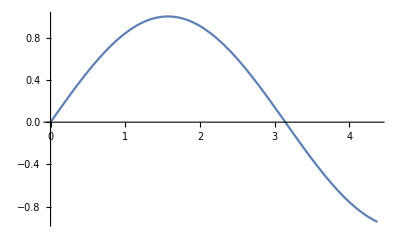

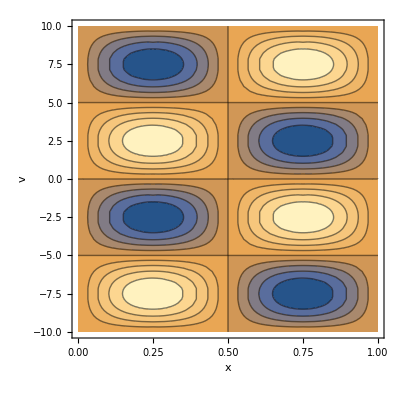

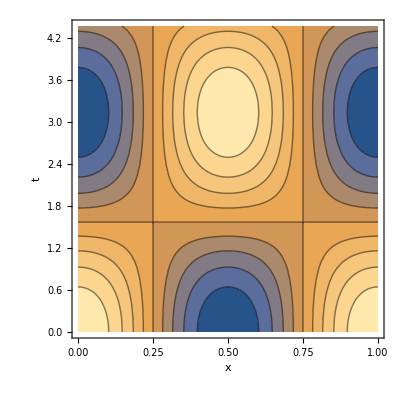

```mathematica
Plot[ft,{t,0,nt dt}]
t=0.1;
ContourPlot[f,{x,Lmin,Lmax},{v,Vmin,Vmax},FrameLabel->Automatic]
ContourPlot[EE,{x,Lmin,Lmax},{t,0,nt dt},FrameLabel->Automatic]
```

continuity1 Test Case

```mathematica
xMin=-1;
xMax=+1;
ft=Sin[w t]; 
fx=Cos[k x];
w=1;
n=2;
v=1;
k=2 Pi/((xMax-xMin)/n);
f=ft fx;
source1=D[f,t]
source2=v D[f,x]
```

Cos[t] Cos[2 π x]

-2 π Sin[t] Sin[2 π x]